```mathematica
Exit
```

```mathematica
n=3;
XX=Table[Indexed[X,i],{i,1,n+1}]
ZZ=Table[Indexed[Z,i],{i,1,n+1}]
YY=Table[Indexed[Y,i],{i,1,n}]
```

{X1,X2,X3,X4}

{Z1,Z2,Z3,Z4}

{Y1,Y2,Y3}

```mathematica
λ=1/(1-XX.ZZ)
λ/.Thread[ZZ->UnitVector[n+1,n+1]]
```

1/(1-X1 Z1-X2 Z2-X3 Z3-X4 Z4)

1/(1-X4)

```mathematica
Φ=(XX-ZZ ZZ.XX)/(1-ZZ.XX)
Φ/.Thread[ZZ->UnitVector[n+1,n+1]]
```

{(X1-Z1 (X1 Z1+X2 Z2+X3 Z3+X4 Z4))/(1-X1 Z1-X2 Z2-X3 Z3-X4 Z4),(X2-Z2 (X1 Z1+X2 Z2+X3 Z3+X4 Z4))/(1-X1 Z1-X2 Z2-X3 Z3-X4 Z4),(X3-Z3 (X1 Z1+X2 Z2+X3 Z3+X4 Z4))/(1-X1 Z1-X2 Z2-X3 Z3-X4 Z4),(X4-Z4 (X1 Z1+X2 Z2+X3 Z3+X4 Z4))/(1-X1 Z1-X2 Z2-X3 Z3-X4 Z4)}

{X1/(1-X4),X2/(1-X4),X3/(1-X4),0}

```mathematica
f=1/Sqrt[2]{Cos[ϕ],Sin[ϕ],Cos[θ],Sin[θ]}

dA=1/2λ^2/.Thread[XX->f]//Simplify

dV=1/3Simplify[
Det[{Φ/.Thread[XX->f],D[Φ/.Thread[XX->f],θ],D[Φ/.Thread[XX->f],ϕ],ZZ}]
]
```

{Cos[ϕ]/(√2),Sin[ϕ]/(√2),Cos[θ]/(√2),Sin[θ]/(√2)}

2/(-2+√2 Cos[ϕ] Z1+√2 Cos[θ] Z3+√2 Z4 Sin[θ]+√2 Z2 Sin[ϕ])^2

(2 √2 (Cos[ϕ] Z1-Cos[θ] Z3-Z4 Sin[θ]+Z2 Sin[ϕ]))/(3 (-2+√2 Cos[ϕ] Z1+√2 Cos[θ] Z3+√2 Z4 Sin[θ]+√2 Z2 Sin[ϕ])^3)

```mathematica
dV2=1/6ZZ.DiagonalMatrix[{-1,-1,1,1}].f/(1-1f.ZZ)^3//Simplify
```

(2 √2 (Cos[ϕ] Z1-Cos[θ] Z3-Z4 Sin[θ]+Z2 Sin[ϕ]))/(3 (-2+√2 Cos[ϕ] Z1+√2 Cos[θ] Z3+√2 Z4 Sin[θ]+√2 Z2 Sin[ϕ])^3)

```mathematica
Z={0,Sin[ψ],0,Cos[ψ]}
```

{0,Sin[ψ],0,Cos[ψ]}

```mathematica
dA//FullSimplify
```

2/(-2+√2 Cos[ψ] Sin[θ]+√2 Sin[ϕ] Sin[ψ])^2

```mathematica
dV2//FullSimplify
```

(2 √2 (-Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ]))/(3 (-2+√2 Cos[ψ] Sin[θ]+√2 Sin[ϕ] Sin[ψ])^3)

```mathematica
Ψ=Φ/.Thread[XX->f]//Simplify
```

{-(√2 Cos[ϕ])/(-2+√2 Cos[ψ] Sin[θ]+√2 Sin[ϕ] Sin[ψ]),(√2 Cos[ψ] (-Cos[ψ] Sin[ϕ]+Sin[θ] Sin[ψ]))/(-2+√2 Cos[ψ] Sin[θ]+√2 Sin[ϕ] Sin[ψ]),-(√2 Cos[θ])/(-2+√2 Cos[ψ] Sin[θ]+√2 Sin[ϕ] Sin[ψ]),(√2 Sin[ψ] (Cos[ψ] Sin[ϕ]-Sin[θ] Sin[ψ]))/(-2+√2 Cos[ψ] Sin[θ]+√2 Sin[ϕ] Sin[ψ])}

```mathematica
R=RotationMatrix[{ZZ,UnitVector[n+1,n+1]}]/.Conjugate->Identity/.Abs->Identity//Simplify
```

{{1,0,0,0},{0,Cos[ψ],0,-Sin[ψ]},{0,0,1,0},{0,Sin[ψ],0,Cos[ψ]}}

```mathematica
R.ZZ//Simplify
```

{0,0,0,1}

```mathematica
h={ϕ,θ,ψ}↦Evaluate[(R.Ψ)⟦1;;n⟧];
Manipulate[
ParametricPlot3D[h[ϕ,θ,ψ],{ϕ,-Pi,Pi},{θ,-Pi,Pi},PlotRange->All,SphericalRegion->True,
MaxRecursion->7,Mesh->{100,100}
],
{ψ,-Pi/4.,Pi/4.}
]
```

```mathematica
dA/.{θ->(θ1+ϕ1)/Sqrt[2],ϕ->(θ1-ϕ1)/Sqrt[2]}
```

2/(-2+√2 Cos[ψ] Sin[(θ1+ϕ1)/(√2)]+√2 Sin[(θ1-ϕ1)/(√2)] Sin[ψ])^2

```mathematica
NA=Function@@{
ψ,
With[{dA=dA},
Quiet@NIntegrate[dA,{ϕ,-Pi,Pi},{θ,-Pi,Pi}]
]
};
NV=Function@@{
ψ,
With[{dV=dV2},
Quiet@NIntegrate[dV,{ϕ,-Pi,Pi},{θ,-Pi,Pi}]
]
};
```

NIntegrate::inumr: The integrand 2/(-2+√2 Cos[ψ] Sin[θ]+√2 Sin[ϕ] Sin[ψ])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.14159,0.},{-3.14159,3.14159}}.

NIntegrate::inumr: The integrand (2 √2 (-Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ]))/(3 (-2+√2 Cos[ψ] Sin[θ]+√2 Sin[ϕ] Sin[ψ])^3) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.14159,0.},{-3.14159,3.14159}}.

```mathematica
DNA=Function@@{
ψ,
With[{dA=D[dA,ψ]//Simplify},
Quiet@NIntegrate[dA,{ϕ,-Pi,Pi},{θ,-Pi,Pi}]
]
};
DNV=Function@@{
ψ,
With[{dV=D[dV2,ψ]//Simplify},
Quiet@NIntegrate[dV,{ϕ,-Pi,Pi},{θ,-Pi,Pi}]
]
};
```

NIntegrate::inumr: The integrand (4 √2 (-Cos[ψ] Sin[ϕ]+Sin[θ] Sin[ψ]))/(-2+√2 Cos[ψ] Sin[θ]+√2 Sin[ϕ] Sin[ψ])^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.14159,0.},{-3.14159,3.14159}}.

NIntegrate::inumr: The integrand -(4 (√2 Cos[ψ] Sin[ϕ]-4 Cos[ψ]^2 Sin[θ] Sin[ϕ]+Sin[θ] Sin[ψ] (√2-4 Sin[ϕ] Sin[ψ])+Sin[θ]^2 Sin[2 ψ]+Sin[ϕ]^2 Sin[2 ψ]))/(3 (-2+√2 Cos[ψ] Sin[θ]+√2 Sin[ϕ] Sin[ψ])^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.14159,0.},{-3.14159,3.14159}}.

```mathematica
DLogV[ψ_]:=DNV[ψ]/NV[ψ]
DLogA[ψ_]:=DNA[ψ]/NA[ψ]
```

```mathematica
IsoperimetricRatio[ψ_?NumericQ]:=36. Pi NV[ψ]^2/NA[ψ]^3
```

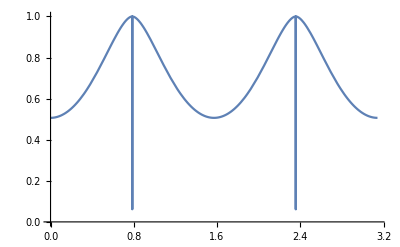

```mathematica
Plot[IsoperimetricRatio[ψ],{ψ,0,Pi}]
```

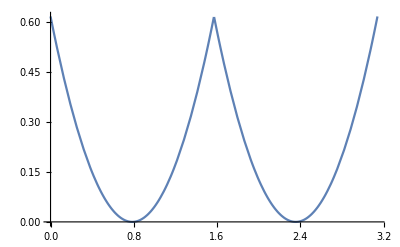

```mathematica
Plot[Min[(ψ-Pi/4)^2,(ψ-3Pi/4)^2],{ψ,0,Pi}]
```